# Individual based model of the joint dynamics of an epidemic and norm-driven NPI on complex networks

## Supplementary Material for Morsky, Magpantay, Day, and Akçay: “The impact of threshold decision mechanisms of collective behaviour on disease spread”

### Approximations for the mean degree and clustering for the social inheritance model derived in Ilany and Akcay (2016, Nature Communications doi:10.1038/ncomms12084)

This does the stationary mean degree. The total number of connections before death is ktot.

```mathematica
Clear[nn,kb,ktot]
```

```mathematica
ktot=kb*nn/2
```

(kb nn)/2

After death, the mean degree of the remaining individuals is slightly lower than kbar.

```mathematica
kbp=2(ktot-kb)/(nn-1)//Simplify
```

(kb (-2+nn))/(-1+nn)

```mathematica
Solve[kb==kbp pn+(nn-2-kbp)pr+pb,kb]//FullSimplify
```

{{kb→-((-1+nn) (pb+(-2+nn) pr))/(1-2 pn+nn (-1+pn-pr)+2 pr)}}

```mathematica
Solve[kb==-((-1+nn) (pb+(-2+nn) pr))/(1-2 pn+nn (-1+pn-pr)+2 pr),pr]/.pb->1//FullSimplify
```

{{pr→(-1+kb+nn+kb nn (-1+pn)-2 kb pn)/((1+kb-nn) (-2+nn))}}

Same result can be found by first picking the individual to reproduce, and killing off another individual at random (and conditioning on whether the dead one is connected to the reproducing one or not).

```mathematica
kbsol=Solve[kb==(nn-1-kb)/(nn-1)(kb pn+(nn-2-kb)pr+1)+kb/(nn-1)((kb-1) pn+(nn-1-kb)pr+1) ,kb][[1]]//FullSimplify
```

{kb→-((-1+nn) (1+(-2+nn) pr))/(1-2 pn+nn (-1+pn-pr)+2 pr)}

This solves for the stationary mean clustering coefficient by equating the number of triangles being destroyed and created by each death and birth, respectively.

Suppose you have an individual with local clustering coefficient cb, and you kill off one of its connections at random. The expected local clustering coefficient of the focal individual is still cb. So killing off an individual at random shouldn’t affect the clustering coefficient of others in the population.

```mathematica
cbp=( cb kb (kb-1)/2-cb(kb-1))/((kb-1)(kb-2)/2)//FullSimplify
```

cb

But you will lose a cbar from the sum for the average clustering because of the death of the individual.

On the other hand, if you add a connection to someone with degree kb and local clustering coeff cb, you can change their LCC, if the expected number of connections to connections added by the newborn is higher. In particular, the difference between the new and old clustering coefficient is given by (where cbn is the number of connections the newborn makes to the focal individuals’ /connections):

```mathematica
cbpp=( cb kb (kb-1)/2+cbn)/((kb+1)(kb)/2)-cb//FullSimplify
```

(2 cbn-2 cb kb)/(kb+kb^2)

Now, we need to calculate cbn separately for each class of the newborn’s (NB) connections: mother, mother’s connections, non-mother’s connections. For the mother (M), it’s easy: the expected number of links to the M’s connections is kb*pn. There is one M.

```mathematica
cbppM=cbpp/.cbn->kb pn//Simplify
```

-(2 (cb-pn))/(1+kb)

For mother's connections (MC), the newborn connects to (kb-1) pn other MCs, each of whom have a probability cb of being connected to a focal MC, so overall, the NB connects to (kb-1) pn cb other MCs. Likewise, the MC is connected to kb/(n-1)*(n-kb-2) non-mother’s connections, (NMC), each of whom have probability pr of being connected to the NB. Finally, the newborn connects to the mother, so the expected cbn is: 1+(kb-1)  pn cb+kb/(n-1) (n-kb-2) pr . There are kb MC.

```mathematica
cbppMC=cbpp/.cbn->1+(kb-1) pn cb+(kbb-cb (kb-1)-1) pr//FullSimplify
```

(2 (1+(-1+kbb) pr+cb (-pn+kb (-1+pn-pr)+pr)))/(kb (1+kb))

Finally, for NMCs, they have on average kb/(n-1)* kb connections to MCs each of whom has a probability pn of being connected to the NB. For the rest, they have kb/(n-1) probability of being connected to the rest of the (nn-kb-3) NMC individals, each of which have a probability pr of connecting to the NB. There are nn-2-kb NMC.

```mathematica
kbb-(kbb-cb (kb-1)-1)*kb/(nn-kb-2)//FullSimplify
```

kbb+(kb (-1+cb-cb kb+kbb))/(2+kb-nn)

```mathematica
cbppNMC=cbpp/.cbn->(kbb-cb (kb-1)-1)*kb/(nn-kb-2)  pn+(kbb+(kb (-1+cb-cb kb+kbb))/(2+kb-nn)) pr//FullSimplify
```

(2 (-cb kb+(kb (1+cb (-1+kb)-kbb) pn)/(2+kb-nn)+(kbb+(kb (-1+cb-cb kb+kbb))/(2+kb-nn)) pr))/(kb (1+kb))

So, the expected change in existing individuals’ clustering coefficients are:

```mathematica
Δcex=cbppM+cbppMC*kb pn+cbppNMC*(nn-kb-2) pr//FullSimplify
```

(2 (2 kb pn+2 kb (-1+kbb) pn pr+(kb-2 kb kbb+kbb (-2+nn)) pr^2+cb kb (-1+kb (-1+pn-pr) (pn-pr)-(pn-pr)^2+2 pr-nn pr)))/(kb (1+kb))

The expected clustering coefficient of the newborn, calculated from the Taylor expansion of the ratio.

```mathematica
tnb=(m mc+cb mc(mc-1)/2+(kbb+(kb (-1+cb-cb kb+kbb))/(2+kb-nn))/(nn-kb-3)  nmc(nmc-1)/2+(kbb-cb (kb-1)-1)/(nn-kb-2) mc nmc);
μtnb=Expectation[tnb,{m\[Distributed]BinomialDistribution[1,pb],mc\[Distributed] BinomialDistribution[kb,pn],nmc\[Distributed] BinomialDistribution[nn-kb-2,pr]}]//FullSimplify;
ttnb=((m+mc+nmc)(m+mc+nmc-1)/2);
μttnb=Expectation[ttnb,{m\[Distributed]BinomialDistribution[1,pb],mc\[Distributed] BinomialDistribution[kb,pn],nmc\[Distributed] BinomialDistribution[nn-kb-2,pr]}]//FullSimplify;
covtttnb=Expectation[(tnb-μtnb)(ttnb-μttnb),{m\[Distributed]BinomialDistribution[1,pb],mc\[Distributed] BinomialDistribution[kb,pn],nmc\[Distributed] BinomialDistribution[nn-kb-2,pr]}]//FullSimplify;
varttnb=Expectation[(ttnb-μttnb)^2,{m\[Distributed]BinomialDistribution[1,pb],mc\[Distributed] BinomialDistribution[kb,pn],nmc\[Distributed] BinomialDistribution[nn-kb-2,pr]}]//FullSimplify;
nbcc=μtnb/μttnb-covtttnb/μttnb^2+varttnb μtnb/μttnb^3 /.pb->1//Simplify;
```

```mathematica
cbsol2=Solve[(Δcex+nbcc)==cb /.{kbb->kbp,kb->kbp},cb][[1]]//Simplify;
```

```mathematica
kbar=kb/.kbsol;
cbar=cb/.cbsol2/.kb->kbar;
```

### Functions for generating networks

networkIterate takes as argument an initial undirected network (variable “init”), entered as a symmetric adjacency matrix where a 1 denotes connection between the individuals corresponding to a row and column, and 0 no connection. It also takes as arguments pn and pr, the probabilities of social inheritance and random connections. The code iterates a death-birth process for “steps” number of times (20-40 times the network size are typically enough time steps for the network to reach a steady state). The output of the function is a list of connections for every individual.

```mathematica
networkIterate[init_,pn_,pr_,steps_]:=Block[{
n=Length[init],
indID=Table[i,{i,1,Length[init]}],
conns=Flatten[Position[#,1]]&/@init,
db, nb,deadconn,inconn,ranconn},
Do[
db = RandomSample[indID, 2];
deadconn=conns[[db[[1]]]];
Do[conns[[deadconn[[i]]]]=Cases[conns[[deadconn[[i]]]],Except[db[[1]]]],{i,Length[deadconn]}];(*Delete the dead individual from everyone's connections*)
inconn=RandomVariate[BinomialDistribution[Length[conns[[db[[2]]]]],pn]];
(*Number of inherited connections*)
ranconn=RandomVariate[BinomialDistribution[n-1-Length[conns[[db[[2]]]]],pr]];(*Number of random Connections*)
nb=Join[RandomSample[conns[[db[[2]]]],inconn],RandomSample[Complement[indID,conns[[db[[2]]]],db],ranconn],{db[[2]]}];(*Draw connection names, also include a connection to the parent*)
Do[AppendTo[conns[[nb[[i]]]],db[[1]]],{i,Length[nb]}];(*Add the new connections of the newborn*)
conns[[db[[1]]]]=nb;(*Replace the dead individual with the newborn*)
,{j,steps}
];
conns
]
```

```mathematica
netsize=10000;
netw=Table[0,{netsize},{netsize}]; (*A blank network*)
```

```mathematica
AbsoluteTiming[conn10K=Monitor[networkIterate[netw,.9,.0002,20*netsize],j];] (*A sample run, for 20 generations; i.e., 20*network size time steps*)
```

{132.515,Null}

We can convert the list of connections back to an adjacency matrix, as below.

```mathematica
toAdjMat[conns_]:=Block[
{adjmat=Table[0,{Length[conns]},{Length[conns]}]},
Do[If[Length[conns[[i]]]>0,Table[adjmat[[i,conns[[i,j]]]]=1,{j,1,Length[conns[[i]]]}],Null],{i,1,Length[conns]}];
adjmat]
```

```mathematica
adjmat=toAdjMat[conn10K];
```

```mathematica
Total/@adjmat//Mean//N (*Average degree of the network*)
```

29.5358

We can check we are at steady state by comparing the mean degree to the analytical approximation for the mean degree from Ilany and Akcay 2016 (derivation in the section above).

```mathematica
-((-1+nn) (1+(-2+nn) pr))/(1-2 pn+nn (-1+pn-pr)+2 pr)/.{nn->netsize,pn->.9,pr->.0002}
```

29.9093

and also comparing it to mean local clustering degree (calculated in the section “Approximations for the mean degree and clustering” above, and also given in Ilany and Akcay 2016)

```mathematica
LocalClusteringCoefficient[AdjacencyGraph[adjmat]]//Mean//N
```

0.300768

```mathematica
cbsol2/.kb->-((-1+nn) (1+(-2+nn) pr))/(1-2 pn+nn (-1+pn-pr)+2 pr)/.{nn->netsize,pn->.9,pr->.0002}
```

{cb→0.296018}

The social inheritance model gives a wider degree distribution than a random network with the same average degree, as depicted below.

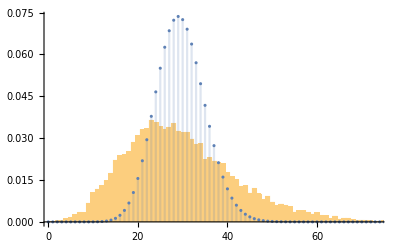

```mathematica
Show[{Histogram[Total/@adjmat,80,"PDF"],DiscretePlot[PDF[BinomialDistribution[10000,29.5358/10000]][x],{x,0,80,1}]}]
```

### Function to run one iteration of the epidemic

Some preliminary functions we will use below.

```mathematica
bestresp[β0_,η_,p_,κ_,inf_,c_,θ_]:=1/(1+Exp[κ(-β0(1-η 0)inf-c*0-θ(p-0)^2-(-β0(1-η 1)inf-c 1-θ(p-1)^2))])(*Best response function from Morsky et al. main text*)
```

```mathematica
awlocalfun[statlist_,conn_]:=(If[Length[#]==0,0,Total[statlist[[#]]]/Length[#]]&/@conn)
awinflocalfun[statlist_,conn_]:=(If[Length[#]==0,0,Count[statlist[[#]],"I"]/Length[#]]&/@conn)
```

```mathematica
awglobalfun[statlist_,conn_]:=Mean[statlist]
awinfglobalfun[statlist_,conn_]:=Count[statlist,"I"]/Length[conn]
```

```mathematica
brInfLBehL[infawlist_,behawlist_,β0_,η_,θ_,c_,κ_,n_]:=Ceiling[RandomReal[{0,1},n]-(1-bestresp[β0,η,#[[1]],κ,#[[2]],c,θ]&/@Transpose[{behawlist,infawlist}])]
brInfLBehG[infawlist_,behawlist_,β0_,η_,θ_,c_,κ_,n_]:=Ceiling[RandomReal[{0,1},n]-(1-bestresp[β0,η,behawlist,κ,#,c,θ]&/@infawlist)]
brInfGBehL[infawlist_,behawlist_,β0_,η_,θ_,c_,κ_,n_]:=Ceiling[RandomReal[{0,1},n]-(1-bestresp[β0,η,#,κ,infawlist,c,θ]&/@behawlist)]
brInfGBehG[infawlist_,behawlist_,β0_,η_,θ_,c_,κ_,n_]:=Ceiling[RandomReal[{0,1},n]-(1-bestresp[β0,η,behawlist,κ,infawlist,c,θ])]
```

A function that takes the network (as an edge list for each node) as an argument, initializes an epidemic and runs it to the end (until only a single infected or exposed individual remains: there is a maximum time to run (1500 time steps)). Options infaw and behaw give the scale of infection and behavioral awareness (0: global, 1: first degree, 2: second degree contacts; default is awareness of second degree contacts)

```mathematica
epidemicrun[conn_,β0_,η_,θ_,c_,κ_,δ_,γ_,OptionsPattern[{infaw->2,behaw->2}]]:=Block[
{n=Length[conn],
connaw,conninfaw,connbehaw,behawfun,infawfun,bestrespfun,
infopt=OptionValue[infaw],(*Infection awareness option. 2 is awareness of infections amongst second order connections, 1 first order, 0, global*)
behopt=OptionValue[behaw],(*Behavioral awareness option. 2 is awareness of infections amongst second order connections, 1 first order, 0, global*)
stat,behstat,disstat,infpress,behawpress,infawpress,inf,beh,exp,trajectory},
(*Preliminaries*)
If[infopt==2||behopt==2,connaw=Table[If[conn[[i]]!={},Union@@Table[conn[[conn[[i,j]]]],{j,1,Length[conn[[i]]]}],{}],{i,1,n}],connaw=conn];
(*Make a list of second order connections, but only if either of the options specify second order connection awareness; otherwise connaw is conn*)
If[infopt==2,conninfaw=connaw,conninfaw=conn];(*If the infection awareness is of second order connections, set the infection awareness list to second order*)
If[behopt==2,connbehaw=connaw,connbehaw=conn];
(*If the behavioral awareness is of second order connections, set the behavior awareness list to second order*)
behawfun=If[behopt==0,awglobalfun,awlocalfun];
infawfun=If[infopt==0,awinfglobalfun,awinflocalfun];
bestrespfun=Which[behopt==0&&infopt==0,brInfGBehG,behopt!=0&&infopt==0,brInfGBehL,behopt==0&&infopt!=0,brInfLBehG,behopt!=0&&infopt!=0,brInfLBehL];

(*Initialization*)
behstat=RandomChoice[{19900,100}->{0,1},n];(*Initial behavioral status, 0 is not masking, 1 is masking*)
disstat=RandomChoice[{19970/20000,10/20000,20/20000,0}->{"S","E","I","R"},n];(*initial fraction of infected individual amongst each individual's connections*)
infawpress=infawfun[disstat,conninfaw];
(*Fraction of infected individuals amongst the infection awareness neighborhood*)
behawpress=behawfun[behstat,connbehaw];
(*Fraction of infected individuals amongst the behavioral awareness neighborhood*)
stat={behstat,disstat,infpress,behawpress,infawpress};(*Collecting all individual status in one matrix: first list is masking status, second list is disease status (string), third is number of infected amongst connections, and fourth is fraction masked amongst second order connections.  This formulation doesn't compute which of the infected ones mask, etc.*)
inf=Count[stat[[2]],"I"]/n;

(*Run the simulation*)
Monitor[trajectory=Reap[Do[
stat[[1]]=bestrespfun[stat[[5]],stat[[4]],β0,η,θ,c,κ,n];(*Update masking behavior, based on the best response function, using the infection and behavioral awareness*)
stat[[2]]=Which[#=="E",RandomChoice[{1.-δ,δ}->{"E","I"}],#=="I",RandomChoice[{1.-γ,γ}->{"I","R"}],True,#]&/@stat[[2]];(*Updating infections: exposed individuals mature to infectious, infectious individuals might mature to recovered *)
stat[[3]]=If[Length[#]==0,0,Count[stat[[2]][[#]],"I"]/Length[#]]&/@conn; (*fraction of infected individual amongst each individual's connections*)
Do[If[stat[[2,i]]=="S",stat[[2,i]]=RandomChoice[{1-β0(1-η*stat[[1,i]])*stat[[3,i]],β0(1-η*stat[[1,i]])*stat[[3,i]]}->{"S","E"}],Null],{i,1,n}];(*New infections (need to think about how to make the rates work out with the discrete simulation)*)
stat[[4]]=behawfun[stat[[1]],connbehaw];
(*Update the social pressure*)
stat[[5]]=infawfun[stat[[2]],conninfaw];
(*Update the infection awareness*)
inf=Count[stat[[2]],"I"]/n;
exp=Count[stat[[2]],"E"]/n;
If[inf+exp>1/n,Null,Break[]];
Sow[{Count[stat[[2]],"S"],Count[stat[[2]],"E"],Count[stat[[2]],"I"],Count[stat[[2]],"R"],Total[stat[[1]]]}] 
(*Trajectories are saved as 5 element lists for each time step: {Susceptibles, Exposed, Infected, Recovered, NPI-adoption frequency}*)
,{j,1500}]][[2,1]],j]
]
```

Sample replicate runs (each run might take a few minutes)

```mathematica
Monitor[testtrajs=Reap[Do[
Sow[epidemicrun[conn10K,.4,.8,.01,.02,1000,.2,.1,infaw->0,behaw->1]],{k,10}]][[2,1]];,k]
```

Plotting trajectories from the replicate runs

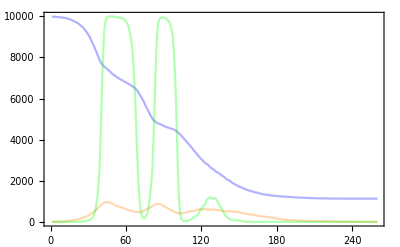

```mathematica
ListPlot[Flatten[Table[testtrajs[[i,All,{1,3,5}]]//Transpose,{i,1,1}],1],Joined->True,PlotRange->All,PlotStyle->{{Blue,Opacity[.3]},{Orange,Opacity[.3]},{Green,Opacity[.3]}},Frame->True]
```

#### Function for plotting the attack rate (to make SI figures)

```mathematica
plotdist[data_,n_,paramit_,OptionsPattern[{list->False,label->"",joined->False,parname->"",ylabel->"",xlabel->"",AspectRatio->Automatic,ImageSize->Medium,BaseStyle->{Black,Directive[FontSize->16,FontFamily->"Helvetica"]}}]]:=Block[{endpoints,listt=OptionValue[list],lab=OptionValue[label],join=OptionValue[joined],paramname=OptionValue[parname],xlab=OptionValue[xlabel],ylab=OptionValue[ylabel],size=OptionValue[ImageSize],a=OptionValue[AspectRatio],sty=OptionValue[BaseStyle]},
If[listt==False,
endpoints=Table[Select[data,#[[1]]==dummy&&Length[#[[2]]]>30&][[All,2]][[All,-1,4]]//N,{dummy,paramit[[1]],paramit[[2]],paramit[[3]]}];
Show[{DistributionChart[endpoints,ChartStyle->{Gray,{Opacity[.2]}},ChartLabels->Table[dummy,{dummy,paramit[[1]],paramit[[2]],paramit[[3]]}],FrameLabel->{xlab,ylab},PlotLabel->lab,BaseStyle->sty],ListPlot[Table[{Table[dum,{Length[endpoints[[dum]]]}],endpoints[[dum]]}//Transpose,{dum,1,Round[(paramit[[2]]-paramit[[1]])/paramit[[3]]]+1,1}],PlotStyle->{{Black,Opacity[.2]}},Joined->join],
ListPlot[Table[{dum,Mean[endpoints[[dum]]]},{dum,1,Round[(paramit[[2]]-paramit[[1]])/paramit[[3]]]+1,1}],PlotStyle->{{Black,PointSize[Large]}}]},ImageSize->size,AspectRatio->a],
endpoints=Table[Select[data,#[[1]]==dummy&&Length[#[[2]]]>30&][[All,2]][[All,-1,4]]//N,{dummy,paramit}];
Show[{DistributionChart[endpoints,ChartStyle->{Gray,{Opacity[.2]}},ChartLabels->Table[dummy,{dummy,paramit}],FrameLabel->{xlab,ylab},PlotLabel->lab,BaseStyle->sty],ListPlot[Table[{Table[dum,{Length[endpoints[[dum]]]}],endpoints[[dum]]}//Transpose,{dum,1,Length[paramit],1}],PlotStyle->{{Black,Opacity[.2]}},Joined->join],
ListPlot[Table[{dum,Mean[endpoints[[dum]]]},{dum,1,Length[paramit],1}],PlotStyle->{{Black,PointSize[Large]}}]},ImageSize->size,AspectRatio->a]]
]
```

The figures in the SI are generated by first generating 10 independent steady-state networks of size 10K (with pn=0.9, and pr=0.0002, giving a mean degree of around 30), and running the epidemicrun[] function above for different values of the parameters on each of the 10 replicate networks.